```mathematica
<<Units`
ppgfttoPSI=0.0519481;
```

```mathematica
LinearEq[pt1_,pt2_]:=Block[{y,x,temp,temp2,temp3},
pt1[[1]]+(y-pt1[[2]])(pt2[[1]]-pt1[[1]])/(pt2[[2]]-pt1[[2]])
];

Interpolate[ycoord_,data_]:=Block[{f,i,y},
For[i=1,i< Length[data],i++,
If[Abs[data[[i,2]]]≤Abs[ycoord]≤ Abs[data[[i+1,2]]],
f=LinearEq[data[[i]],data[[i+1]]];
Return[f/.y->ycoord];
];
];
];
```

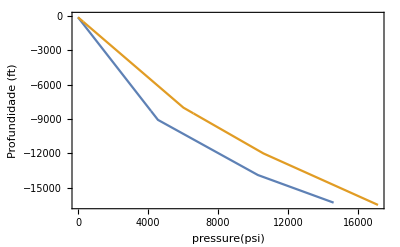

```mathematica
dataporepressure={{8.33,-100},{9.7,-9066},{14.25,-13885},{17.25,-16300}};
PtsFracPressure={{9,-100},{14.5,-6025.97},{17,-12000},{20,-16500}};
dataporepressure={{0,-100},{4568.32,-9066},{10278.50,-13885},{14606.48,-16300}};
PtsFracPressure={{0,-100},{6025.97,-8000},{10597.39,-12000},{17142.84,-16500}};
tabpore=Table[{Interpolate[y,dataporepressure],y},{y,-16300,0}];
tabfrac=Table[{Interpolate[y,PtsFracPressure],y},{y,-16500,0}];
ListLinePlot[{tabpore,tabfrac},Frame->True,FrameLabel->{{" Profundidade (ft) "," "},{"pressure(psi)"," Janela Operacional "}},LabelStyle->Directive[Bold,14],Axes->None]
```

```mathematica
MakeCompatibleSizeVectors[refinedvec_,coarsevecl_,coarsevecvar_]:=Block[{newvec,y0,y1,x0,x1,counter,i},
newvec={};
counter=1;
If[Length[coarsevecl]!=Length[coarsevecvar],
Print["Não é possível realizar o refinamento, os vetores coarse devem ter o mesmo tamanho."];
];
For[i=1,i<Length[coarsevecl],i++,
(*If[i>=Length[coarsevecvar],Break[]];*)
y0=coarsevecvar[[i]];
y1=coarsevecvar[[i+1]];
x0=coarsevecl[[i]];
x1=coarsevecl[[i+1]];
While[(coarsevecl[[i]]<=refinedvec[[counter]]<=coarsevecl[[i+1]])&&counter<Length[refinedvec],
AppendTo[newvec,N[(y1-y0)/(x1-x0) (refinedvec[[counter]]-x0)+y0]];
counter++;
];
If[i==Length[coarsevecl]-1,AppendTo[newvec,N[(y1-y0)/(x1-x0) (refinedvec[[counter]]-x0)+y0]]];
];
newvec//N
]
```

```mathematica
(*refina de n divisões de refl até lf*)
refine[l0_,lf_,refl_,n_]:=Block[{dref,standardref=100,refinedvec,lastcoarsedata,i},
refinedvec=Table[dl//N,{dl,l0,refl,(refl-l0)/standardref}];
lastcoarsedata=refl;
If[Abs[lf-refl]<10^-8,
dref=(lf-l0)/n;
refinedvec={};
lastcoarsedata=l0;
,
dref=(lf-refl)/n;
lastcoarsedata=refl;
];

For[i=1,i≤n,i++,
AppendTo[refinedvec,lastcoarsedata//N];
lastcoarsedata+=dref;
];
AppendTo[refinedvec,N[lf]];
refinedvec//N
]
```

```mathematica
L0=0.;
LF=14800.;
LtoRef=14799;
nrefs=50.;
refinedl=refine[L0,LF,LtoRef,nrefs];
```

```mathematica
Length[refinedl]
```

152

Dado PI e PO, rint e rext, faz o cálculo da tensão radial e tangencial

```mathematica
ComputeRadialAndTangetialStress[r_,ri_,re_,PI_,PO_]:=Block[{sigr,sigtheta},
sigr=(PI (r^2-re^2) ri^2+PO re^2 (-r^2+ri^2))/(r^2 (re^2-ri^2));
sigtheta=(PI(r^2+re^2) ri^2-PO re^2 (r^2+ri^2))/(r^2 (re^2-ri^2));
{sigr,sigtheta}//N
];
ComputeRadialAndTangetialStress2[r_,ri_,re_,PI_,PO_,FZ_]:=Block[{ez,sigrr,sigtt,sigzz,a,b,Pa,Pb,nu=0.30,young=3 10^7},
a=ri;
b=re;
Pa=PI;
Pb=PO;
ez=FZ/(Pi young(b^2-a^2))-(2nu)/young(Pa a^2 -Pb b^2)/(b^2-a^2);
sigrr=(Pa a^2 -Pb b^2)/(b^2-a^2)-(a^2 b^2 (Pa-Pb))/((b^2-a^2)r^2);
sigtt=(Pa a^2 -Pb b^2)/(b^2-a^2)+(a^2 b^2 (Pa-Pb))/((b^2-a^2)r^2);
sigzz=2 nu (Pa a^2 -Pb b^2)/(b^2-a^2)+young ez;
{sigrr,sigtt,sigzz}//N
];
(*di=12.376;
de=14;
{sigr,sigt,sigz}=ComputeRadialAndTangetialStress2[di/2 ,di/2,de/2,8237,3629,1.312705856587157*^6]
sigz Pi/4( de^2-di^2)*)
```

Dado dint, dext, PI e PO, faz o cálculo da tensão axial (TA) devido ao efeito poisson (Balão)

```mathematica
ComputeFballoning[di_,de_,Pint_,Pext_,nu_]:=Block[{sigr,sigt,Fballoning},
{sigr,sigt}=ComputeRadialAndTangetialStress[di/2 ,di/2,de/2,Pint,Pext];
Fballoning=nu(sigr+sigt)Pi/4( de^2-di^2);
Fballoning//N
];
```

```mathematica
ComputeFtemperature[de_,di_,TM_,TPM_]:=Block[{young = 3 10^7,alfa=6.9 10^-6,ΔT,T1,f,fp,T2,Ftemperature},
ΔT= (TPM-TM) ;
Ftemperature=-young alfa ΔT Pi/4(de^2-di^2);
Ftemperature//N
]
```

```mathematica
ComputeFBend[de_,di_,θ_]:=Block[{young = 3. 10^7,area,Fbend},
area=Pi/4. (de^2. -di^2.);
Fbend=Pi young de θ/(100. 360. 12.) area;
Fbend//N(*resultado em lb*)
]
```

```mathematica
di=19.124;
de=20;
ComputeFBend[de,di,2]
```

234901.

```mathematica
ComputeInitialForce[InternalPressIni_,ExternalPressIni_,Lvec_,PipeData_]:=Block[{Lcement,Fpiston,sz,di,de,alfa,nu,young,w,Ai,Ao,i,lacum=0.,Fi},
{di,de,alfa,nu,young,w,Lcement}=PipeData;(*dados do tubular*)
Ai=Pi/4 di^2;(*área interna*)
Ao=Pi/4 de^2;(*área externa*)
sz=Length[Lvec];
Fi=Table[0,{sz}];
Fpiston=(InternalPressIni[[sz]] Ai-ExternalPressIni[[sz]] Ao);(*Força Pistão*)
Fi[[sz]]=Fpiston;
For[i=sz-1,i≥1,i--,
lacum+=(-Lvec[[i]]+Lvec[[i+1]]);
Fi[[i]]=Fpiston+w lacum;(*Força axial inicial total*)
];

Fi//N
]
```

```mathematica
ComputeInitialForce[InternalPressIni_,ExternalPressIni_,Lvec_,PipeData_,doglegdata_]:=Block[{Lcement,Fpiston,sz,di,de,alfa,nu,young,w,Ai,Ao,i,lacum=0.,Fi},
{di,de,alfa,nu,young,w,Lcement}=PipeData;(*dados do tubular*)
Ai=Pi/4 di^2;(*área interna*)
Ao=Pi/4 de^2;(*área externa*)
sz=Length[Lvec];
Fi=Table[0,{sz}];
Fpiston=(InternalPressIni[[sz]] Ai-ExternalPressIni[[sz]] Ao);(*Força Pistão*)
Fi[[sz]]=Fpiston;
For[i=sz-1,i≥1,i--,
lacum+=(-Lvec[[i]]+Lvec[[i+1]]);
Fi[[i]]=Fpiston+w lacum+ComputeFBend[de,di,doglegdata[[i]]];(*Força axial inicial total*)
];

Fi//N
]
```

```mathematica
ComputeForces[InternalPressinitial_,ExternalPressinitial_,InternalPressKick_,ExternalPressKick_,Ti_,Tf_,Lvec_,PipeData_]:=Block[{Lcement,Fi,Fballoning,Ftemp,flag,Ffreemean,sz,di,de,alfa,nu,young,w,Ai,Ao,i,lacum=0.,Ffinal,ΔInternalPress,ΔExternalPress},
(*Calcula a força devido as condições iniciais*)
Fi=ComputeInitialForce[InternalPressinitial,ExternalPressinitial,Lvec,PipeData];
ΔInternalPress=InternalPressKick-InternalPressinitial;
ΔExternalPress=ExternalPressKick-ExternalPressinitial;
Print["Length[InternalPressKick] = ",Length[InternalPressKick]];
Print["Length[InternalPressinitial] = ",Length[InternalPressinitial]];
Print["Length[ExternalPressKick] = ",Length[ExternalPressKick]];
Print["Length[ExternalPressinitial] = ",Length[ExternalPressinitial]];
{di,de,alfa,nu,young,w,Lcement}=PipeData;
Ai=Pi/4 di^2;
Ao=Pi/4 de^2;
sz=Length[ΔInternalPress];
Ffreemean=0.;
(*Calcula a força devido ao efeito poisson ou balão*)
Fballoning=ComputeFballoning[di,de,#1,#2,nu]&[ΔInternalPress,ΔExternalPress];
(*Calcula a força devido ao efeito térmico*)
Ftemp=ComputeFtemperature[de,di,#1,#2]&[Ti,Tf];
Ffinal=Table[0,{sz}];
Ffinal[[sz]]=Fi[[sz]]+Fballoning[[sz]]+Ftemp[[sz]];
For[i=sz-1,i≥1,i--,
lacum+=Lvec[[i+1]]-Lvec[[i]];
If[lacum-(Lvec[[sz]]-Lcement)<=0,
(*Trecho Cimentado*)
Ffinal[[i]]=Fi[[i]]+Fballoning[[i]]+Ftemp[[i]];
flag=True;
,
(*Trecho Livre*)
If[flag==True,
(*No primeiro passo do trecho livre calcula a média das forças de temperatura e balão somente do trecho livre*)
Ffreemean=(Sum[Fballoning[[j]],{j,1,i}]+Sum[Ftemp[[j]],{j,1,i}])/i;
flag=False;
];
Ffinal[[i]]=Ffreemean+Fi[[i]];
];
];
{Fi,Ffinal}//N
]
```

```mathematica
ComputeForces[InternalPressinitial_,ExternalPressinitial_,InternalPressKick_,ExternalPressKick_,Ti_,Tf_,Lvec_,PipeData_,doglegdata_]:=Block[{Lcement,Fi,Fballoning,Ftemp,flag,Ffreemean,sz,di,de,alfa,nu,young,w,Ai,Ao,i,lacum=0.,Ffinal,ΔInternalPress,ΔExternalPress},
(*Calcula a força devido as condições iniciais*)
Fi=ComputeInitialForce[InternalPressinitial,ExternalPressinitial,Lvec,PipeData,doglegdata];
ΔInternalPress=InternalPressKick-InternalPressinitial;
ΔExternalPress=ExternalPressKick-ExternalPressinitial;
Print["Length[InternalPressKick] = ",Length[InternalPressKick]];
Print["Length[InternalPressinitial] = ",Length[InternalPressinitial]];
Print["Length[ExternalPressKick] = ",Length[ExternalPressKick]];
Print["Length[ExternalPressinitial] = ",Length[ExternalPressinitial]];
{di,de,alfa,nu,young,w,Lcement}=PipeData;
Ai=Pi/4 di^2;
Ao=Pi/4 de^2;
sz=Length[ΔInternalPress];
Ffreemean=0.;
(*Calcula a força devido ao efeito poisson ou balão*)
Fballoning=ComputeFballoning[di,de,#1,#2,nu]&[ΔInternalPress,ΔExternalPress];
(*Calcula a força devido ao efeito térmico*)
Ftemp=ComputeFtemperature[de,di,#1,#2]&[Ti,Tf];
Ffinal=Table[0,{sz}];
Ffinal[[sz]]=Fi[[sz]]+Fballoning[[sz]]+Ftemp[[sz]];
For[i=sz-1,i≥1,i--,
lacum+=Lvec[[i+1]]-Lvec[[i]];
If[lacum-(Lvec[[sz]]-Lcement)<=0,
(*Trecho Cimentado*)
Ffinal[[i]]=Fi[[i]]+Fballoning[[i]]+Ftemp[[i]];
flag=True;
,
(*Trecho Livre*)
If[flag==True,
(*No primeiro passo do trecho livre calcula a média das forças de temperatura e balão somente do trecho livre*)
Ffreemean=(Sum[Fballoning[[j]],{j,1,i}]+Sum[Ftemp[[j]],{j,1,i}])/i;
flag=False;
];
Ffinal[[i]]=Ffreemean+Fi[[i]];
];
];
{Fi,Ffinal}//N
]
```

Calcula a resistência do tubular à ruptura e ao colapso de acordo com a API BUL 5C3

```mathematica
ComputePipeStrength[siga_,sigy_,de_,di_,young_,nu_]:=Block[{t=(de-di)/2,BurstStrength, ColapseStrength,dt,Ypa,A,B,C,F,G,range1,range2,range3},
BurstStrength=0.875 2 sigy/(de/t);
dt=de/t;
Ypa=sigy (Sqrt[1-3/4 (siga/sigy)^2]-1/2 siga/sigy);
A=2.8762+0.10679 10^-5 Ypa+0.21301 10^-10 Ypa^2-0.53132 10^-16 Ypa^3;
B=0.026233+0.50609 10^-6 Ypa;
C=-465.93+0.030867 Ypa-0.10483 10^-7 Ypa^2+0.36989 10^-13 Ypa^3;
F=(46.95 10^6 ((3(B/A))/(2+B/A))^3)/(Ypa((3(B/A))/(2+B/A)-B/A)(1-(3(B/A))/(2+B/A))^2);
G=F B/A;
range1=(2+B/A)/(3 B/A);

If[dt≥ range1,

ColapseStrength=(2 young)/(1-nu^2) 1/(dt(dt-1)^2);
];
range2=(Ypa(A-F))/(C+Ypa(B-G));
If[range2≤ dt≤ range1,

ColapseStrength= (F/dt-G)Ypa;
];
range3=(Sqrt[(A-2)^2+8(B+C/Ypa)]+(A-2))/(2(B+C/Ypa));
If[(range3≤ dt≤ range2),

ColapseStrength=Ypa (A/dt-B)-C;
];

If[dt≤ range3,

ColapseStrength=2Ypa (dt-1)/dt^2;
];
{BurstStrength,ColapseStrength}//N
];
```

Calcula a tensão de von Mises

```mathematica
ComputeVonMises[sigr_,sigt_,siga_]:=Block[{sig,S,J2,vm,teste},
sig={{sigr,0,0},{0,sigt,0},{0,0,siga}};

S=sig-1/3 Tr[sig] IdentityMatrix[3];
J2=1/2 Tr[S.S];
Sqrt[3 J2]
];
```

```mathematica
ComputeVonMises[sigr,sigt,siga]
```

√(3/2) √((siga+1/3 (-siga-sigr-sigt))^2+(sigr+1/3 (-siga-sigr-sigt))^2+(1/3 (-siga-sigr-sigt)+sigt)^2)

```mathematica
√(3/2) √((siga+1/3 (-siga-sigr-sigt))^2+(sigr+1/3 (-siga-sigr-sigt))^2+(1/3 (-siga-sigr-sigt)+sigt)^2)//Simplify
```

√(siga^2+sigr^2-sigr sigt+sigt^2-siga (sigr+sigt))

1.3 Pressão resistente de Klever Stewart

```mathematica
ComputeBurstResistance[n_,de_,t_,fu_,sa_,po_]:=Block[{kdr,kr,puts,pref,Futs,pfactor,pfactorNeck,pM,pBurstKS,pburst},
kdr=0.5^(n+1)+(1/√3)^(n+1);
kr=(4^(1-n)-1)*3^(n-1);
puts=(2 kdr t fu)/(de- t);
pref=(0.5^n*puts)/2(((2/√3)^(n+1))+1);
Futs=Pi t  fu(de-t);
pfactor=Sqrt[1-kr*(sa/fu)^2];
pfactorNeck=√((1-sa^2/fu^2)/(-3^(1-n)+4^(1-n)));
pM=pref pfactor;
pBurstKS=po+Min[pM,(pM+0.5^n puts)/2];
If[sa/fu≤ ((√3)/2)^(1-n),
If[pM≤ (pM+0.5^n puts)/2,
pburst=po+pM;
,
pburst= po+(pM+0.5^n puts)/2;
],
pburst=po+pref*pfactorNeck;
];
pburst//N
];
```

1.3 Pressão resistente de Klever Tamano

```mathematica
Hfunc[ov_,ec_,rs_,fy_]:=Max[0,0.127 ov+0.0039ec+0.440 rs/fy];
Hfunc[ov_,ec_,rs_]:=Max[0,0.127 ov+0.0039ec-0.440 rs];
ComputeColapseStrengthKT[siga_,sigy_,pi_,d_,t_,young_,nu_,ov_,ec_,rs_]:=Block[{ke=1,sol,H,deltapec,deltapy,deltapmises,deltaptresca,ky=1,eq,po,Fa,Feff,Fy,Ai,Ao,As,kdr,BurstStrength, ColapseStrength,pyc,pec,pym,xi,Si,dt,c,val},

deltaptresca=ky 2 sigy t/(d-t);
deltapmises=Sqrt[(ky(4./√3.)sigy t/(d-t))^2 (1.-(siga/(ky sigy))^2)];
deltapy=Min[(deltapmises+deltaptresca)/2,deltapmises];
(*deltapy=(deltapmises+deltaptresca)/2;*)
deltapec=ke (2. young)/(1.-nu^2)1./((d/t)(d/t-1.)^2);
H=Hfunc[ov,ec,rs];
ColapseStrength=pi+(2. deltapy deltapec)/(deltapy+deltapec+Sqrt[(deltapy-deltapec)^2 +4. H deltapy deltapec]);
ColapseStrength

]
```

Calcula os fatores de segurança

```mathematica
ComputeSafetyFactors[PipeData_,AxialForce_,Pint_,Pext_,ov_,ec_,rs_]:=Block[{KTStress,KSstress,KSSF={},KTSF={},APISF={}, BarlowSF={},i,barlow,api,de,di,young,nu,weigthperfeet,L1,L2,pipe=1,sigy,VMSF={},sigr,sigt,area,VMStress},

{de,di,young,nu,weigthperfeet,L1,L2,sigy}=PipeData[[pipe]];
For[i=Length[Pint]-1,i>1,i--,
If[L1>Pint[[i,2]],
pipe++;
{de,di,young,nu,weigthperfeet,L1,L2,sigy}=PipeData[[pipe]];
];
{sigr,sigt}=ComputeRadialAndTangetialStress[di/2,di/2,de/2,Pint[[i,1]],Pext[[i,1]]];
area=Pi/4 (de^2 -di^2);


VMStress=ComputeVonMises[sigr,sigt,AxialForce[[i,1]]/area];
KSstress=ComputeBurstResistance[1,de,0.5(de -di),sigy,AxialForce[[i,1]]/area,Pext[[i,1]]];
KTStress=ComputeColapseStrengthKT[AxialForce[[i,1]]/area,sigy,Pint[[i,1]],de,0.5(de -di),young,nu,ov,ec,rs];
api=ComputePipeStrength[AxialForce[[i,1]]/area,sigy,de,di,young,nu];
If[burst==True,
deltap=(Pint[[i,1]]-Pext[[i,1]]);
,
deltap=(-Pint[[i,1]]+Pext[[i,1]]);
];
AppendTo[BarlowSF,{api[[1]]/deltap,-Pint[[i,2]]}];
AppendTo[APISF,{api[[2]]/deltap,-Pint[[i,2]]}];
AppendTo[VMSF,{sigy/VMStress,-Pint[[i,2]]}];
AppendTo[KSSF,{KSstress/deltap,-Pint[[i,2]]}];
AppendTo[KTSF,{KTStress/deltap,-Pint[[i,2]]}];
];
{BarlowSF,APISF,VMSF,KSSF,KTSF}
];
```

# MUD DROP DUE TO LOST RETURNS

# -Graphics-

```mathematica
burst=False;
lvec={0,100,951,1901,2100,2100,2581,2851,2995,3409,3801,3823,4237,4651,4751,5065,5479,5700,5893,6307,6650,6721,7135,7549,7600,7963,8377,8550,8791,9066,9205,9500,9500,9618,9700,9700,9950,10032,10400,10446,10850,10860,11274,11300,11688,11750,12102,12200,12516,12650,12930,13100,13344,13550,13758,13885,14000,14100,14172,14200,14300,14400,14500,14586,14600,14700,14800,14900,15000};
InternalPressLostCirc={1.36,1.36,1.36,1.37,1.37,1.37,1.37,246.55,377.70,754.03,1110.09,1130.36,1506.70,1883.03,1973.64,2259.36,2635.70,2837.18,3012.03,3388.36,3700.72,3764.69,4141.03,4517.36,4564.27,4893.69,5270.03,5427.82,5646.36,5896.81,6022.69,6291.27,6291.45,6399.03,6473.09,6473.27,6700.45,6775.36,7109.54,7151.69,7518.63,7528.02,7904.36,7927.72,8280.69,8336.81,8657.02,8745.90,9033.36,9154.99,9409.69,9564.08,9786.02,9973.17,10162.35,10277.71,10382.26,10473.17,10538.69,10564.08,10654.99,10745.90,10836.81,10915.02,10927.72,11018.63,11109.53,11200.44,11291.26};
ExternalPressLostCirc={0.00,74.49,715.43,1430.94,1580.91,1581.06,1943.30,2146.45,2255.12,2566.93,2861.96,2878.76,3190.58,3502.39,3577.47,3814.21,4126.04,4292.98,4437.85,4749.67,5008.49,5061.49,5373.31,5685.13,5724.00,5996.95,6308.76,6439.51,6620.59,6828.10,6932.40,7154.94,7155.92,7245.04,7306.41,7306.57,7494.80,7556.87,7833.76,7868.69,8172.72,8180.50,8492.32,8511.68,8804.15,8850.64,9115.96,9189.60,9427.78,9528.56,9739.60,9867.52,10051.41,10206.48,10363.23,10458.82,10545.44,10620.77,10675.05,10696.09,10771.42,10846.74,10922.07,10986.87,10997.39,11072.72,11148.04,11223.37,11298.62};
AxialForceLostCircWellCat={572652,567361,521838,471018,460366,460355,434627,420198,412480,390333,369379,368186,346038,323891,318559,301744,279597,267739,257450,235302,216920,213155,191008,168861,166100,146713,124566,115281,102419,87680,80272,64461,78890,73268,69395,69396,57528,53616,36166,33965,14805,14315,-5338,-6558,-24987,-27917,-44637,-49278,-64289,-70641,-83941,-92002,-103591,-113363,-123240,-129264,-134602,-139149,-142425,-143695,-148241,-152788,-157326,-161215,-161846,-166366,-170886,-175406,-179926};
lvecini={0,951,1901,2100,2100,2851,3801,4751,5700,6650,7600,8550,9500,9500,9501,9700,9700,9950,10400,10850,11300,11750,12200,12650,13100,13550,14000,14100,14200,14300,14400,14500,14600,14700,14800,14900,15000};
AxialForceInitialWellCat={616757,565942,515123,504471,504460,464303,413483,362664,311844,261025,210205,159385,108566,108566,108539,97866,97866,84491,60416,36341,12266,-11809,-35884,-59959,-84034,-108110,-132185,-137535,-142885,-148235,-153585,-158935,-164285,-169635,-174985,-180335,-185685};
AxialForceInitialWellCat=MakeCompatibleSizeVectors[lvec,lvecini,AxialForceInitialWellCat];
InternalPressinitial={0.88,716.30,1431.80,1581.77,1581.92,2147.30,2862.80,3578.30,4293.80,5009.30,5724.80,6440.30,7155.73,7155.88,7156.18,7306.39,7306.54,7494.80,7833.80,8172.70,8511.70,8850.60,9189.60,9528.60,9867.50,10206.50,10545.40,10620.80,10696.10,10771.40,10846.70,10922.10,10997.40,11072.70,11148.00,11223.40,11298.62};
InternalPressinitial=MakeCompatibleSizeVectors[lvec,lvecini,InternalPressinitial];
ExternalPressinitial={0.88,716.30,1431.80,1581.77,1581.92,2147.30,2862.80,3578.30,4293.80,5009.30,5724.80,6440.30,7155.73,7155.88,7156.18,7309.50,7309.65,7501.80,7847.80,8193.75,8539.70,8885.70,9231.70,9577.65,9923.60,10269.60,10615.60,10697.65,10779.70,10861.80,10943.90,11025.95,11108.00,11190.10,11272.20,11354.30,11436.32};
ExternalPressinitial=MakeCompatibleSizeVectors[lvec,lvecini,ExternalPressinitial];
Ti=Table[0,{i,1,Length[lvec]}];
Tf=Table[0,{i,1,Length[lvec]}];


vmsfwellcat={2.172,2.168,2.109,1.994,1.894,1.939,1.964,2.040,2.117,2.122,2.210,2.307,2.331,2.412,2.527,2.593,2.653,2.793,2.921,2.949,3.122,3.318,3.344,3.539,3.793,3.910,4.085,4.305,4.425,4.705,4.488,4.589,4.660,4.660,4.896,4.978,5.385,5.441,5.983,5.998,6.682,6.730,7.542,7.690,8.656,8.969,10.157,10.759,12.286,13.442,15.543,17.903,21.146,23.771,26.723,29.896,32.692,33.922,39.196,46.402,56.813,70.297,73.107,100,100,100,100};
colapsesfwellcat={100,69.549,7.439,3.836,2.883,2.927,2.951,3.020,3.085,3.089,3.159,3.229,3.246,3.300,3.372,3.411,3.445,3.519,3.581,3.594,3.669,3.746,3.756,3.824,3.903,3.936,3.983,4.037,4.065,4.124,4.107,4.130,4.146,4.146,4.195,4.212,4.286,4.295,4.378,4.381,4.462,4.466,4.529,4.539,4.597,4.614,4.668,4.692,4.742,4.772,4.817,4.856,4.895,4.920,4.942,4.962,4.976,4.981,5.001,5.021,5.042,5.059,5.062,5.083,5.103,5.124,5.145};

(*Refinamento da solução*)
refinedl=Table[dl,{dl,0,15000,200}];
InternalPressinitial=MakeCompatibleSizeVectors[refinedl,lvec,InternalPressinitial];
ExternalPressinitial=MakeCompatibleSizeVectors[refinedl,lvec,ExternalPressinitial];
AxialForceInitialWellCat=MakeCompatibleSizeVectors[refinedl,lvec,AxialForceInitialWellCat];
AxialForceLostCircWellCat=MakeCompatibleSizeVectors[refinedl,lvec,AxialForceLostCircWellCat];
InternalPressLostCirc=MakeCompatibleSizeVectors[refinedl,lvec,InternalPressLostCirc];
ExternalPressLostCirc=MakeCompatibleSizeVectors[refinedl,lvec,ExternalPressLostCirc];
Ti=MakeCompatibleSizeVectors[refinedl,lvec,Ti];
Tf=MakeCompatibleSizeVectors[refinedl,lvec,Tf];

newlvec={0,100,950,1900,2581,2850,2995,3409,3800,3823,4237,4651,4750,5065,5479,5700,5893,6307,6650,6721,7135,7549,7600,7963,8377,8550,8791,9066,9205,9500,9500,9618,9700,9700,9950,10032,10400,10446,10850,10860,11274,11300,11688,11750,12102,12200,12516,12650,12930,13100,13344,13550,13758,13885,14000,14100,14172,14200,14300,14400,14500,14586,14600,14700,14800,14900,15000};




vmsfwellcat=MakeCompatibleSizeVectors[refinedl,newlvec,vmsfwellcat];
colapsesfwellcat=MakeCompatibleSizeVectors[refinedl,newlvec,colapsesfwellcat];

lvec=refinedl;

vmsfwellcatwithl=Table[{vmsfwellcat[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
colapsesfwellcatwithl=Table[{colapsesfwellcat[[i]],-lvec[[i]]},{i,1,Length[lvec]}];


lcimento=9500.01;
di=8.535;
de=9.625;
alfa=6.9 10^-6;
nu=0.30;
young=3 10^7;
weightperfeet=53.5;
sigy=80000;
PipeData={di,de,alfa,nu,young,weightperfeet,lcimento};
{Fi,Ffim}=ComputeForces[InternalPressinitial,ExternalPressinitial,InternalPressLostCirc,ExternalPressLostCirc,Ti,Tf,lvec,PipeData];
ComputedFi=Table[{Fi[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
ComputedFfim=Table[{Ffim[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
WellCatFi=Table[{AxialForceInitialWellCat[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
WellCatFfim=Table[{AxialForceLostCircWellCat[[i]],-lvec[[i]]},{i,1,Length[lvec]}];

InternalPressinitialPlot=Table[{InternalPressinitial[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
ExternalPressinitialPlot=Table[{ExternalPressinitial[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
diffini=Table[{ExternalPressinitial[[i]]-InternalPressinitial[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
InternalPressLostCircPlot=Table[{InternalPressLostCirc[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
ExternalPressLostCircPlot=Table[{ExternalPressLostCirc[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
difffim=Table[{ExternalPressLostCirc[[i]]-InternalPressLostCirc[[i]],-lvec[[i]]},{i,1,Length[lvec]}];


pressaoini=ListLinePlot[{InternalPressinitialPlot,ExternalPressinitialPlot,diffini},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"Pressão (psi)",""}},PlotLegends->{"P_i","P_o","P_i-P_o"},PlotStyle->{Dashed,Red,Dotted},PlotMarkers->{"○", "□", "◇"}]
pressaosobrevi=ListLinePlot[{InternalPressLostCircPlot,ExternalPressLostCircPlot,difffim},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"Pressão (psi)",""}},PlotLegends->{"P_i","P_o","P_i-P_o"},PlotStyle->{Dashed,Red,Dotted},PlotMarkers->{"○", "□", "◇"}]


forcaini=ListLinePlot[{WellCatFi,ComputedFi},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"Força Axial Inicial (lbf)",""}},PlotLegends->{"WellCat","Calculada"},PlotStyle->{Dashed,Red},PlotMarkers->{ "○", "◇"}]
(*Export["C:\\Users\\Diogo\\Dropbox\\figs\\compara05ftcimentofini.jpg",compara,ImageResolution->300]*)

forcafim=ListLinePlot[{WellCatFfim,ComputedFfim},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"Força Axial Final (lbf)",""}},PlotLegends->{"WellCat","Calculada"},PlotStyle->{Dashed,Red},PlotMarkers->{ "○", "◇"},PlotRange->All]

pipedata={de,di,young,nu,weightperfeet};
pipedatavec={
{de,di,young,nu,weightperfeet,lvec[[1]],lvec[[Length[lvec]]],sigy}
};
PiData=Table[{InternalPressLostCirc[[i]],lvec[[i]]},{i,1,Length[lvec]}];
PeData=Table[{ExternalPressLostCirc[[i]],lvec[[i]]},{i,1,Length[lvec]}];
ax=Table[{Ffim[[i]],lvec[[i]]},{i,1,Length[lvec]}];
{barlowsf,apisf,vmsf,kssf,ktsf}=ComputeSafetyFactors[pipedatavec,ax,PiData,PeData,0.66,13.2,-0.264];

vmsfplot=ListLinePlot[{vmsfwellcatwithl,vmsf},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"Fator de Segurança - von Mises(Triaxial)",""}},PlotLegends->{"von Mises WellCat","von Mises Calculado"},PlotStyle->{Dashed,Red},PlotMarkers->{"○", "□"}]
kssfplot=ListLinePlot[{ktsf,apisf,colapsesfwellcatwithl},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"fator de Segurança ao Colapso",""}},PlotLegends->{"Klever Tamano Calculado","API Calculado","Fator de Segurança ao Colapso - WellCat"},PlotStyle->{Dashed,Red,Dotted},PlotMarkers->{"○", "□", "◇"}]
```

Length[InternalPressKick] = 76

Length[InternalPressinitial] = 76

Length[ExternalPressKick] = 76

Length[ExternalPressinitial] = 76

-Graphics-

-Graphics-

-Graphics-

-Graphics-

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics-

-Graphics-

3.3 Equação de estado limite de Klever-Tamano

## 3.3.1 Vetor gradiente

```mathematica
ComputeGrad[siga_,sigy_,pint_,pext_,de_,t_,young_,nu_,X1_,X2_,X3_,X4_,X5_,X6_,X7_,X8_,X9_]:=Block[{NofD,x7,nYieldStrength,x3,PintofD,x8,nDe,nt,x2,nYoung,nNu,x4,x5,x6,x1,PextofD,x9,gx,grad,subst},
gx= x1*ComputeColapseStrengthKT[NofD*x7,nYieldStrength*x3,PintofD*x8,nDe,nt*x2,nYoung,nNu,x4,x5,x6]-(PextofD*x9-PintofD*x8);
grad= {{D[gx,x1],D[gx,x2],D[gx,x3],D[gx,x4],D[gx,x5],D[gx,x6],D[gx,x7],D[gx,x8],D[gx,x9]}};
subst={NofD->siga,nYieldStrength->sigy,PintofD->pint,nDe->de,nt->t,nYoung->young,nNu->nu,PextofD->pext,x1->X1,x2->X2,x3->X3,x4->X4,x5->X5,x6->X6,x7->X7,x8->X8,x9->X9};

{{gx},grad}/.subst
];
```

```mathematica
CreateRVDataVC[RVdata_]:=Block[{rvvec={},rvdata,i,RVX={}},

For[i=1,i≤Length[RVdata],i++,
rvdata=Table[0,13];
rvdata[[1]]=RVdata[[i,1]];
rvdata[[2]]=RVdata[[i,2]];
rvdata[[3]]=RVdata[[i,3]];
rvdata[[4]]=RVdata[[i,4]];
AppendTo[RVX, CALCPAR[rvdata]];

];
RVX
]
```

## 3.3.2 Montagem do problema

```mathematica
SolVector={};
IndiceConfiabilidade[PiData_,PeData_,AxialForceData_,CasingData_,RandomVarsData_]:=Block[{CsVsBeta,i,area},

CsVsBeta={};
nDe=CasingData[[1]];
nDi=CasingData[[2]];
nt=nDe-nDi;
nYoung=CasingData[[3]];
nNu=CasingData[[4]];
nYieldStrength=CasingData[[8]];
area=Pi/4 (nDe^2 - nDi^2);

For[i=1,i≤Length[PiData],i++,

PintofD =PiData[[i,1]]; (* Nominal Internal Pressure at depth D in psi *)
PextofD =PeData[[i,1]]; (* Nominal External Pressure at depth D in psi *)
NofD=AxialForceData[[i,1]] /area ;(* Nominal Axial Load at depth D in psi*)

NRV=Length[RandomVarsData];
RVX=CreateRVDataVC[RandomVarsData];

NLS = 1;

NP = 20;
CDFLIMPLOT=10^-2.5;
PRINT = False;
ClearAll[vx,fx,GX,GRADX,X1,X2,X3,X4,X5,X6,X7,X8,X9];

SetLimitStateVectors[NRV];

DesignPoint = Table[DPCREATE,{NLS}];
LSPARALLEL = False;
BuildRVParameterVectors[RVX];
print=ComputeGrad[NofD,nYieldStrength,PintofD,PextofD,nDe,nt,nYoung,nNu,X1,X2,X3,X4,X5,X6,X7,X8,X9];
(*If[i==1,
Print["g,gradg = ",print];
];*)
GX[fx]:=ComputeGrad[NofD,nYieldStrength,PintofD,PextofD,nDe,nt,nYoung,nNu,X1,X2,X3,X4,X5,X6,X7,X8,X9][[1]];
GRADX[fx]:=ComputeGrad[NofD,nYieldStrength,PintofD,PextofD,nDe,nt,nYoung,nNu,X1,X2,X3,X4,X5,X6,X7,X8,X9][[2]];


GAUSSIAN = True;
Do[If[TYPE[[k]]≠ "NORMAL"&&TYPE[[k]]≠ "DETERM",
GAUSSIAN = False],{k,1,NRV}];

RX=IdentityMatrix[NRV];

If[Det[RX]== 1,CORRELATED =False,CORRELATED = True];

cov = Table[RX[[k,w]]*SDEV[[k]]*SDEV[[w]],{k,1,NRV},{w,1,NRV}];

ClearAll[Jyz,Jzy,Jzx,Jxz,Jxy,Jyx];

{Jyz,Jzy} = JacobYZ[RX];
{Jxz,Jzx} = JacobXZ[RVX,MEAN];

Jyx = Jyz.Jzx;
Jxy = Jxz.Jzy;

(* 4. Busca pelo ponto de projeto e índice de confiabilidade *)

ConvergenceCrit = {100,"DELTA_BETA",10^-3,0,0};

xh = Table[0,{NLS}];
yh = Table[0,{NLS}];
vg = Table[0,{NLS}];

Do[
FindDesignPoint[lsn];
,{lsn,1,NLS}];

BETA = DPGET[DesignPoint[[1]],{"BETA"}];
ALFA = DPGET[DesignPoint[[1]],{"ALFA"}];

(*AppendTo[SolVector,{revestimento,-data[[w]][[2]],selectedTube,PextofD,PintofD,NofD,data[[w]][[1]],BETA}];*)
AppendTo[CsVsBeta,{BETA,-PiData[[i,2]]}];
];
CsVsBeta
];
```

```mathematica
CsVsBeta=IndiceConfiabilidade[PiData,PeData,ax,pipedatavec,KTRandomVarsData]
```

{{14.9366,0},{13.8625,-200},{13.1306,-400},{12.596,-600},{12.1826,-800},{11.8486,-1000},{11.5694,-1200},{11.3295,-1400},{11.1185,-1600},{10.9295,-1800},{10.7573,-2000},{10.598,-2200},{10.4497,-2400},{10.363,-2600},{10.7507,-2800},{11.0835,-3000},{11.3721,-3200},{11.6248,-3400},{11.8482,-3600},{12.0471,-3800},{12.2257,-4000},{12.3868,-4200},{12.533,-4400},{12.6663,-4600},{12.7884,-4800},{12.9008,-5000},{13.0047,-5200},{13.101,-5400},{13.1906,-5600},{13.2742,-5800},{13.3523,-6000},{13.4257,-6200},{13.4947,-6400},{13.5599,-6600},{13.6214,-6800},{13.6797,-7000},{13.735,-7200},{13.7877,-7400},{13.838,-7600},{13.8858,-7800},{13.9316,-8000},{13.9754,-8200},{14.0176,-8400},{14.0581,-8600},{14.0969,-8800},{14.1345,-9000},{14.1707,-9200},{14.2057,-9400},{14.2368,-9600},{14.2699,-9800},{14.3021,-10000},{14.3334,-10200},{14.3637,-10400},{14.3934,-10600},{14.4223,-10800},{14.4505,-11000},{14.4781,-11200},{14.505,-11400},{14.5313,-11600},{14.5571,-11800},{14.5825,-12000},{14.6073,-12200},{14.6317,-12400},{14.6557,-12600},{14.6792,-12800},{14.7025,-13000},{14.7254,-13200},{14.7479,-13400},{14.7702,-13600},{14.7922,-13800},{14.8139,-14000},{14.8355,-14200},{14.8568,-14400},{14.8779,-14600},{14.8988,-14800},{14.9196,-15000}}

```mathematica
ListLinePlot[{ktsf,CsVsBeta},Frame->True,FrameLabel->{{" Depth (ft)","Surface Casing"},{"safety factor and reliability index(β) "," Critical Case: Kick - Assumption: Partial full of gas - Failure check: Klever-Tamano"}},PlotLegends->{"safety factor","reliability index(β)"},PlotStyle->{Dashed,Red},PlotMarkers->{"○", "□"}]
```

-Graphics-

# 7’’ PRODUTICTION TIEBACK Evacuated Casing -Graphics-

```mathematica
burst=False;
lvec={0,100,1480,2960,4440,5920,7400,8880,9066,10360,11840,13320,13885,14800};
InternalPressinitial={0.09,90.91,1345.50,2690.90,4036.40,5381.80,6727.30,8072.70,8241.80,9418.20,10763.60,12109.10,12622.71,13454.41};
ExternalPressinitial={0.09,90.91,1345.45,2690.90,4036.35,5381.80,6727.25,8072.70,8241.79,9418.15,10763.60,12109.05,12622.68,13454.41};
AxialForceInitialWellCat={414946,411149,358709,302469,246229,189989,133749,77509,70441,21269,-34971,-91211,-112681,-147451};


AxialForceEvacuatedCasingWellCat={303906,300110,247670,191430,135190,78950,22710,-33530,-40598,-89770,-146010,-202250,-223720,-258490};
InternalPressEvacuatedCasing={0.00,0.05,0.77,1.54,2.31,3.08,3.84,4.61,4.71,5.38,6.15,6.92,7.21,7.74};
ExternalPressEvacuatedCasing={0.09,90.91,1345.45,2690.91,4036.36,5381.81,6727.27,8072.72,8241.81,9418.17,10763.62,12109.07,12622.71,13454.44};

Ti=Table[0,{i,1,Length[lvec]}];
Tf=Table[0,{i,1,Length[lvec]}];

vmsfwellcat={3.426,3.423,3.228,2.820,2.394,2.032,1.744,1.517,1.492,1.337,1.193,1.075,1.036,0.977};
axialsfwellcat={3.426,3.469,4.204,5.439,7.701,13.187,45.843,31.050,25.644,11.597,7.130,5.148,4.654,4.028};
colapsesfwellcat={100,100,8.646,4.503,3.114,2.414,1.980,1.665,1.631,1.427,1.249,1.110,1.065,0.999};





(*Refinamento da solução*)
(*refinedl=Table[dl,{dl,0,14800,10}];*)
L0=0.;
LF=14800.;
lcimento=14799.1;
nrefs=1000.;
refinedl=refine[L0,LF,lcimento,nrefs];
InternalPressinitial=MakeCompatibleSizeVectors[refinedl,lvec,InternalPressinitial];
ExternalPressinitial=MakeCompatibleSizeVectors[refinedl,lvec,ExternalPressinitial];
AxialForceInitialWellCat=MakeCompatibleSizeVectors[refinedl,lvec,AxialForceInitialWellCat];
AxialForceEvacuatedCasingWellCat=MakeCompatibleSizeVectors[refinedl,lvec,AxialForceEvacuatedCasingWellCat];
InternalPressEvacuatedCasing=MakeCompatibleSizeVectors[refinedl,lvec,InternalPressEvacuatedCasing];
ExternalPressEvacuatedCasing=MakeCompatibleSizeVectors[refinedl,lvec,ExternalPressEvacuatedCasing];
Ti=MakeCompatibleSizeVectors[refinedl,lvec,Ti];
Tf=MakeCompatibleSizeVectors[refinedl,lvec,Tf];


vmsfwellcat=MakeCompatibleSizeVectors[refinedl,lvec,vmsfwellcat];
axialsfwellcat=MakeCompatibleSizeVectors[refinedl,lvec,axialsfwellcat];
colapsesfwellcat=MakeCompatibleSizeVectors[refinedl,lvec,colapsesfwellcat];

lvec=refinedl;

vmsfwellcatwithl=Table[{vmsfwellcat[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
colapsesfwellcatwithl=Table[{colapsesfwellcat[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
axialsfwellcatwithl=Table[{axialsfwellcat[[i]],-lvec[[i]]},{i,1,Length[lvec]}];

di=6.094;
de=7;
alfa=6.9 10^-6;
nu=0.30;
young=3 10^7;
weightperfeet=38;
sigy=95000;
PipeData={di,de,alfa,nu,young,weightperfeet,lcimento};
{Fi,Ffim}=ComputeForces[InternalPressinitial,ExternalPressinitial,InternalPressEvacuatedCasing,ExternalPressEvacuatedCasing,Ti,Tf,lvec,PipeData];
ComputedFi=Table[{Fi[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
ComputedFfim=Table[{Ffim[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
WellCatFi=Table[{AxialForceInitialWellCat[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
WellCatFfim=Table[{AxialForceEvacuatedCasingWellCat[[i]],-lvec[[i]]},{i,1,Length[lvec]}];


InternalPressinitialPlot=Table[{InternalPressinitial[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
ExternalPressinitialPlot=Table[{ExternalPressinitial[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
diffini=Table[{ExternalPressinitial[[i]]-InternalPressinitial[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
InternalPressEvacuatedCasingPlot=Table[{InternalPressEvacuatedCasing[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
ExternalPressEvacuatedCasingPlot=Table[{ExternalPressEvacuatedCasing[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
difffim=Table[{ExternalPressEvacuatedCasing[[i]]-InternalPressEvacuatedCasing[[i]],-lvec[[i]]},{i,1,Length[lvec]}];


pressaoini=ListLinePlot[{InternalPressinitialPlot,ExternalPressinitialPlot,diffini},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"Pressão (psi)",""}},PlotLegends->{"P_i","P_o","P_i-P_o"},PlotStyle->{Dashed,Red,Dotted},PlotMarkers->{"○", "□", "◇"}]
pressaosobrevi=ListLinePlot[{InternalPressEvacuatedCasingPlot,ExternalPressEvacuatedCasingPlot,difffim},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"Pressão (psi)",""}},PlotLegends->{"P_i","P_o","P_i-P_o"},PlotStyle->{Dashed,Red,Dotted},PlotMarkers->{"○", "□", "◇"}]

forcaini=ListLinePlot[{WellCatFi,ComputedFi},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"Força Axial Inicial (lbf)",""}},PlotLegends->{"WellCat","Calculada"},PlotStyle->{Dashed,Red},PlotMarkers->{ "○", "◇"},PlotRange->All]
(*Export["C:\\Users\\Diogo\\Dropbox\\figs\\compara05ftcimentofini.jpg",compara,ImageResolution->300]*)

forcafim=ListLinePlot[{WellCatFfim,ComputedFfim},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"Força Axial Final (lbf)",""}},PlotLegends->{"WellCat","Calculada"},PlotStyle->{Dashed,Red},PlotMarkers->{ "○", "◇"},PlotRange->All]

pipedata={de,di,young,nu,weightperfeet};
pipedatavec={
{de,di,young,nu,weightperfeet,lvec[[1]],lvec[[Length[lvec]]],sigy}
};
PiData=Table[{InternalPressEvacuatedCasing[[i]],lvec[[i]]},{i,1,Length[lvec]}];
PeData=Table[{ExternalPressEvacuatedCasing[[i]],lvec[[i]]},{i,1,Length[lvec]}];
ax=Table[{Ffim[[i]],lvec[[i]]},{i,1,Length[lvec]}];
{barlowsf,apisf,vmsf,kssf,ktsf}=ComputeSafetyFactors[pipedatavec,ax,PiData,PeData,0.66,13.2,-0.264];

vmsfplot=ListLinePlot[{vmsfwellcatwithl,vmsf},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"Fator de Segurança - von Mises(Triaxial)",""}},PlotLegends->{"von Mises WellCat","von Mises Calculado"},PlotStyle->{Dashed,Red},PlotMarkers->{"○", "□"},PlotRange->All]
ktsfplot=ListLinePlot[{ktsf,apisf,colapsesfwellcatwithl},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"fator de Segurança ao Colapso",""}},PlotLegends->{"Klever Tamano Calculado","API Calculado","Fator de Segurança ao Colapso - WellCat"},PlotStyle->{Dashed,Red,Dotted},PlotMarkers->{"○", "□", "◇"},PlotRange->{{0,10},{-14800,0}}]
```

Length[InternalPressKick] = 1102

Length[InternalPressinitial] = 1102

Length[ExternalPressKick] = 1102

Length[ExternalPressinitial] = 1102

-Graphics-

-Graphics-

-Graphics-

-Graphics-

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics-

-Graphics-

```mathematica
burst=True;
lvec={0,100,1040,1900,1980,2100,2100,2920,3800,3860,4800,5700,5740,6680,7600,7620,8560,9500,9500,9501,9700,9700,9950,10400,10850,11300,11750,12200,12650,13100,13550,14000,14100,14200,14300,14400,14500,14600,14700,14800,14900,15000};
InternalPressinitial={0.05,75.30,783.40,1431.20,1491.40,1581.72,1581.87,2199.50,2862.35,2907.50,3615.60,4293.50,4323.60,5031.70,5724.65,5739.70,6447.80,7155.73,7155.88,7156.18,7306.39,7306.54,7494.80,7833.80,8172.70,8511.70,8850.60,9189.60,9528.60,9867.50,10206.50,10545.40,10620.80,10696.10,10771.40,10846.70,10922.10,10997.40,11072.70,11148.00,11223.40,11298.62};
ExternalPressinitial={0.05,75.30,783.35,1431.20,1491.40,1581.71,1581.87,2199.45,2862.35,2907.50,3615.55,4293.50,4323.60,5031.65,5724.65,5739.70,6447.75,7155.73,7155.88,7156.18,7309.50,7309.65,7501.80,7847.80,8193.75,8539.70,8885.70,9231.70,9577.65,9923.60,10269.60,10615.60,10697.65,10779.70,10861.80,10943.90,11025.95,11108.00,11190.10,11272.20,11354.30,11436.32};
AxialForceInitialWellCat={616810,611466,561176,515161,510886,504471,504460,460596,413512,410306,360016,311863,309726,259436,210215,209146,158856,108566,108566,108539,97866,97866,84491,60416,36341,12266,-11809,-35884,-59959,-84034,-108110,-132185,-137535,-142885,-148235,-153585,-158935,-164285,-169635,-174985,-180335,-185685};


InternalPressKick={454.64,545.46,1400.00,2181.89,2254.55,2363.55,2363.73,3109.09,3909.15,3963.64,4818.18,5636.40,5672.73,6527.27,7363.65,7381.82,8236.36,9090.81,9091.00,9091.36,9272.63,9272.81,9500.00,9909.09,10318.18,10727.27,11136.36,11545.45,11954.54,12363.63,12772.72,13181.81,13272.72,13363.63,13454.54,13545.45,13636.36,13727.26,13818.17,13909.08,13999.99,14090.81};
ExternalPressKick={279.52,354.77,1062.80,1710.64,1770.84,1861.15,1861.30,2478.87,3141.76,3186.91,3894.94,4572.88,4602.98,5311.01,6004.00,6019.05,6727.08,7435.04,7155.75,7156.05,7242.34,7242.42,7350.56,7545.29,7740.02,7934.74,8129.47,8324.20,8518.92,8713.65,8908.38,9103.10,9146.38,9189.65,9232.92,9276.19,9319.47,9362.74,9406.01,9449.28,9492.56,9535.79};
AxialForceKickWellCat={640998,635653,585363,539349,535073,528659,528648,484783,437700,434493,384203,336051,333913,283623,234402,233333,183043,132753,171933,171916,165304,165308,157033,142140,127247,112352,97462,82569,67675,52782,37890,23120,20011,16902,13793,10684,7583,4500,1418,-1665,-4748,-7831};
Ti=Table[0,{i,1,Length[lvec]}];
Tf=Table[0,{i,1,Length[lvec]}];
lcimento=9500.01;
di=8.535;
de=9.625;
alfa=6.9 10^-6;
nu=0.30;
young=3 10^7;
weightperfeet=53.5;
PipeData={di,de,alfa,nu,young,weightperfeet,lcimento};
{Fi,Ffim}=ComputeForces[InternalPressinitial,ExternalPressinitial,InternalPressKick,ExternalPressKick,Ti,Tf,lvec,PipeData];
ComputedFi=Table[{Fi[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
ComputedFfim=Table[{Ffim[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
WellCatFi=Table[{AxialForceInitialWellCat[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
WellCatFfim=Table[{AxialForceKickWellCat[[i]],-lvec[[i]]},{i,1,Length[lvec]}];


InternalPressinitialPlot=Table[{InternalPressinitial[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
ExternalPressinitialPlot=Table[{ExternalPressinitial[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
diffini=Table[{ExternalPressinitial[[i]]-InternalPressinitial[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
InternalPressKickPlot=Table[{InternalPressKick[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
ExternalPressKickPlot=Table[{ExternalPressKick[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
difffim=Table[{InternalPressKick[[i]]-ExternalPressKick[[i]],-lvec[[i]]},{i,1,Length[lvec]}];
pipedatavec={
{de,di,young,nu,weightperfeet,lvec[[1]],lvec[[Length[lvec]]],sigy}
};

pressaoini=ListLinePlot[{InternalPressinitialPlot,ExternalPressinitialPlot,diffini},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"Pressão (psi)",""}},PlotLegends->{"P_i","P_o","P_i-P_o"},PlotStyle->{Dashed,Red,Dotted},PlotMarkers->{"○", "□", "◇"}]
pressaosobrevi=ListLinePlot[{InternalPressKickPlot,ExternalPressKickPlot,difffim},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"Pressão (psi)",""}},PlotLegends->{"P_i","P_o","P_i-P_o"},PlotStyle->{Dashed,Red,Dotted},PlotMarkers->{"○", "□", "◇"}]

forcaini=ListLinePlot[{WellCatFi,ComputedFi},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"Força Axial Inicial (lbf)",""}},PlotLegends->{"WellCat","Calculada"},PlotStyle->{Dashed,Red},PlotMarkers->{ "○", "◇"}]
(*Export["C:\\Users\\Diogo\\Dropbox\\figs\\compara05ftcimentofini.jpg",compara,ImageResolution->300]*)

forcafim=ListLinePlot[{WellCatFfim,ComputedFfim},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"Força Axial Final (lbf)",""}},PlotLegends->{"WellCat","Calculada"},PlotStyle->{Dashed,Red},PlotMarkers->{ "○", "◇"}]
(*Export["C:\\Users\\Diogo\\Dropbox\\figs\\compara6000ftcimentofkick.jpg",compara,ImageResolution->300]*)

ax=Table[{Ffim[[i]],lvec[[i]]},{i,1,Length[lvec]}];
InternalPressKickPlot=Table[{InternalPressKick[[i]],lvec[[i]]},{i,1,Length[lvec]}];
ExternalPressKickPlot=Table[{ExternalPressKick[[i]],lvec[[i]]},{i,1,Length[lvec]}];
{barlowsf,apisf,vmsf,kssf,ktsf}=ComputeSafetyFactors[pipedatavec,ax,InternalPressKickPlot,ExternalPressKickPlot,0.66,13.2,-0.264];

kssfplot=ListLinePlot[{kssf,barlowsf},Frame->True,FrameLabel->{{"Profundidade (feet)",""},{"fator de Segurança ao Colapso",""}},PlotLegends->{"Klever Tamano Calculado","API Calculado","Fator de Segurança ao Colapso - WellCat"},PlotStyle->{Dashed,Red,Dotted},PlotMarkers->{"○", "□", "◇"}]
```

Length[InternalPressKick] = 42

Length[InternalPressinitial] = 42

Length[ExternalPressKick] = 42

Length[ExternalPressinitial] = 42

-Graphics-

-Graphics-

-Graphics-

-Graphics-

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics-

3.2 Equação de estado limite de Klever-Stewart

```mathematica
ComputeBurstResistance[n_,de_,t_,fu_,sa_,po_]:=Block[{kdr,kr,puts,pref,Futs,pfactor,pfactorNeck,pM,pBurstKS,pburst},
kdr=0.5^(n+1)+(1/√3)^(n+1);
kr=(4^(1-n)-1)*3^(n-1);
puts=(2 kdr t fu)/(de- t);
pref=(0.5^n*puts)/2(((2/√3)^(n+1))+1);
Futs=Pi t  fu(de-t);
pfactor=Sqrt[1-kr*(sa/fu)^2];
pfactorNeck=√((1-sa^2/fu^2)/(-3^(1-n)+4^(1-n)));
pM=pref pfactor;
pBurstKS=po+Min[pM,(pM+0.5^n puts)/2];
pBurstKS

];
```

```mathematica
ComputeGrad[n_,de_,t_,fu_,sa_,pi_,po_,X1_,X2_,X3_,X4_,X5_,X6_]:=Block[{NofD,x7,nYieldStrength,x3,PintofD,x8,nDe,nt,x2,nYoung,nNu,x4,x5,x6,x1,PextofD,x9,gx,grad,subst},
gx= x1*ComputeBurstResistance[n,x4*de,x2*t,x3*fu,sa,x5*po]-x6 pi;
grad= {{D[gx,x1],D[gx,x2],D[gx,x3],D[gx,x4],D[gx,x5],D[gx,x6]}};
subst={x1->X1,x2->X2,x3->X3,x4->X4,x5->X5,x6->X6};

{{gx},grad}/.subst
];
```

```mathematica
IndiceConfiabilidade[PiData_,PeData_,AxialForceData_,CasingData_,RandomVarsData_,kns_]:=Block[{CsVsBeta,KSRandomVars,area,w},

CsVsBeta={};
nDe=CasingData[[1]];
nDi=CasingData[[2]];
nt=nDe-nDi;
nYoung=CasingData[[3]];
nNu=CasingData[[4]];
nYieldStrength=CasingData[[8]];
area=Pi/4 (nDe^2 - nDi^2);

For[w=1,w≤Length[PiData],w++,
PintofD =PiData[[w,1]]; (* Nominal Internal Pressure at depth D in psi *)
PextofD = PeData[[w,1]]; (* Nominal External Pressure at depth D in psi *)
NofD=AxialForceData[[w,1]]/area ; (* Nominal Axial Load at depth D in psi*)

KSnfactor=kns;

NRV=Length[RandomVarsData];
RVX=CreateRVDataVC[RandomVarsData];

nUltimateStrength= 1.1875 nYieldStrength;
NLS = 1;

NP = 20;
CDFLIMPLOT=10^-2.5;
PRINT = False;
ClearAll[vx,fx,GX,GRADX,X1,X2,X3,X4,X5,X6];

SetLimitStateVectors[NRV];

DesignPoint = Table[DPCREATE,{NLS}];

LSPARALLEL = False;
BuildRVParameterVectors[RVX];

GX[fx] :=ComputeGrad[KSnfactor,nDe,nt*X2,nUltimateStrength*X3,NofD*X4,PintofD*X6,PextofD*X5,X1,X2,X3,X4,X5,X6][[1]];
GRADX[fx] := ComputeGrad[KSnfactor,nDe,nt*X2,nUltimateStrength*X3,NofD*X4,PintofD*X6,PextofD*X5,X1,X2,X3,X4,X5,X6][[2]];

GAUSSIAN = True;
Do[If[TYPE[[i]]≠ "NORMAL"&&TYPE[[i]]≠ "DETERM",
GAUSSIAN = False],{i,1,NRV}];

RX=IdentityMatrix[NRV];

If[Det[RX]== 1,CORRELATED =False,CORRELATED = True];

cov = Table[RX[[i,j]]*SDEV[[i]]*SDEV[[j]],{i,1,NRV},{j,1,NRV}];

ClearAll[Jyz,Jzy,Jzx,Jxz,Jxy,Jyx];

{Jyz,Jzy} = JacobYZ[RX];
{Jxz,Jzx} = JacobXZ[RVX,MEAN];

Jyx = Jyz.Jzx;
Jxy = Jxz.Jzy;

(* 4. Busca pelo ponto de projeto e índice de confiabilidade *)

ConvergenceCrit = {100,"DELTA_BETA",10^-3,0,0};

xh = Table[0,{NLS}];
yh = Table[0,{NLS}];
vg = Table[0,{NLS}];

Do[
FindDesignPoint[lsn];
,{lsn,1,NLS}];

BETA = DPGET[DesignPoint[[1]],{"BETA"}];
ALFA = DPGET[DesignPoint[[1]],{"ALFA"}];

AppendTo[CsVsBeta,{BETA,-PiData[[w,2]]}];
];
CsVsBeta
];
```

```mathematica
KSRandomVarsData={{"meKS","NORMAL",1.004,0.047*1.004},{"APIyield","NORMAL",1.1,0.0422*1.1},{"Thickness","NORMAL",1.0069,0.0259*1.0069},{"Nax","DETERM",1.0,0.3},{"Pext","DETERM",1.0,0.01},{"Pint","DETERM",1.0,0.01}};
```

```mathematica
CsVsBeta=IndiceConfiabilidade[InternalPressKickPlot,ExternalPressKickPlot,ax,pipedatavec[[1]],KSRandomVarsData,0.104]
```

{{20.9285,0},{20.8577,-100},{20.1722,-1040},{19.5125,-1900},{19.4495,-1980},{19.3551,-2100},{19.355,-2100},{18.6988,-2920},{17.9911,-3800},{17.9433,-3860},{17.2109,-4800},{16.5509,-5700},{16.5227,-5740},{15.8878,-6680},{15.3192,-7600},{15.3074,-7620},{14.7757,-8560},{14.2869,-9500},{14.1745,-9500},{14.1649,-9501},{14.0394,-9700},{14.0393,-9700},{13.8838,-9950},{13.6111,-10400},{13.3462,-10850},{13.0887,-11300},{12.8379,-11750},{12.5946,-12200},{12.3579,-12650},{12.1274,-13100},{11.8998,-13550},{11.6632,-14000},{11.6155,-14100},{11.5885,-14200},{11.5411,-14300},{11.494,-14400},{11.4471,-14500},{11.4005,-14600},{11.3542,-14700},{11.3081,-14800},{11.2622,-14900},{11.2166,-15000}}

```mathematica
ListLinePlot[{kssf,CsVsBeta},Frame->True,FrameLabel->{{" Depth (ft)","Surface Casing"},{"safety factor and reliability index(β) "," Critical Case: Kick - Assumption: Partial full of gas - Failure check: Klever-Stewart"}},PlotLegends->{"safety factor","reliability index(β)"},PlotStyle->{Dashed,Red},PlotMarkers->{"○", "□"}]
```

-Graphics-